### Start choosing the example:

```mathematica
t=7;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{}|>

```mathematica
(rule=CriticalCongestionSolver2[d2e=D2E[Data/.{I1->2,U1->5,U2->1}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

(Maybe the) system is not feasible!

            	Check the paper: The current method for stationary mean-field games on networks

Done!

{0.097075,<|u1→5,u2→3,u3→3,u4→3,u5→3,u6→1,u7→5,u8→5,u9→1,u10→1,u11→5,u12→5,j1→0,j2→2,j3→0,j4→0,j5→0,j6→2,j7→0,j8→0,j9→0,j10→2,j11→0,j12→2|>}

```mathematica
(rule=CriticalCongestionSolver2[d2e])//AbsoluteTiming
```

EliminateVarsSimplify for the us

(Maybe the) system is not feasible!

            	Check the paper: The current method for stationary mean-field games on networks

Done!

{0.0381,<|u1→5,u2→3,u3→3,u4→3,u5→3,u6→1,u7→5,u8→5,u9→1,u10→1,u11→5,u12→5,j1→0,j2→2,j3→0,j4→0,j5→0,j6→2,j7→0,j8→0,j9→0,j10→2,j11→0,j12→2|>}

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->2,U1->5,U2->1}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 0.059764 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.084137,Null}

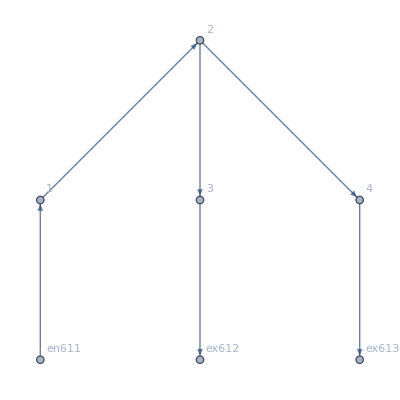

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→5.,u639→3.,u640→3.,u641→5.,u642→1.,u643→5.,u644→3.,u645→3.,u646→1.,u647→5.,u648→1.,u649→5.|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→3.09306,u639→2.04653,u640→2.04653,u641→5.,u642→1.,u643→3.09306,u644→2.04653,u645→2.04653,u646→1.,u647→5.,u648→1.,u649→3.09306|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.46461×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.46461×10^-16

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→3.19814,u639→2.09907,u640→2.09907,u641→5.,u642→1.,u643→3.19814,u644→2.09907,u645→2.09907,u646→1.,u647→5.,u648→1.,u649→3.19814|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→3.44322,u639→2.22161,u640→2.22161,u641→5.,u642→1.,u643→3.44322,u644→2.22161,u645→2.22161,u646→1.,u647→5.,u648→1.,u649→3.44322|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→4.66698,u639→2.83349,u640→2.83349,u641→5.,u642→1.,u643→4.66698,u644→2.83349,u645→2.83349,u646→1.,u647→5.,u648→1.,u649→4.66698|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is Min[3.14018×10^-15,ComplexInfinity]

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→5.,u639→3.,u640→3.,u641→5.,u642→1.,u643→5.,u644→3.,u645→3.,u646→1.,u647→5.,u648→1.,u649→5.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→5.88529,u639→3.44265,u640→3.44265,u641→5.,u642→1.,u643→5.88529,u644→3.44265,u645→3.44265,u646→1.,u647→5.,u648→1.,u649→5.88529|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.70336×10^-16

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 2.70336×10^-16

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→8.28546,u639→4.64273,u640→4.64273,u641→5.,u642→1.,u643→8.28546,u644→4.64273,u645→4.64273,u646→1.,u647→5.,u648→1.,u649→8.28546|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.157511

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.157511

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.157511

«7 more identical outputs»

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→9.16909,u639→4.82336,u640→4.82336,u641→5.,u642→1.,u643→9.16909,u644→4.82336,u645→4.81093,u646→1.,u647→5.,u648→1.,u649→9.16909|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.742103

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.742103

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 0.742103

«7 more identical outputs»

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→10.0898,u639→3.09887,u640→3.09887,u641→5.,u642→1.,u643→10.0898,u644→3.09887,u645→1.22705,u646→1.,u647→5.,u648→1.,u649→10.0898|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«7 more identical outputs»

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→12.8941,u639→3.,u640→3.,u641→5.,u642→1.,u643→12.8941,u644→3.,u645→-4.89413,u646→1.,u647→5.,u648→1.,u649→12.8941|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

FRX1: The Minimum between the Error and the relative Errors on the nonlinear terms is 1.

«17 more identical outputs»

<|j614→2.,j615→0,j616→2.,j617→0.,j618→2.,j619→2.,j620→0.,j621→0.,j622→0.,j623→0.,j624→0.,j625→0.,jt626→0.,jt627→2.,jt628→0,jt629→2.,jt630→0.,jt631→0.,jt632→0.,jt633→0.,jt634→0.,jt635→0.,jt636→2.,jt637→0.,u638→19.3732,u639→3.,u640→3.,u641→5.,u642→1.,u643→19.3732,u644→3.,u645→-11.3732,u646→1.,u647→5.,u648→1.,u649→19.3732|>